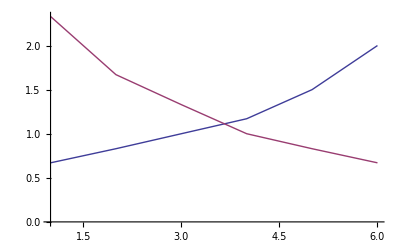

```mathematica
hSize = {{1,0.67},{2,0.83},{3,1},{4,1.17},{5,1.5},{6,2}};
hMargin = {{1,2.33},{2,1.67},{3,1.33},{4,1},{5,.83},{6,.67}};
ListLinePlot[{hSize,hMargin}]
```

```mathematica
nlmSize = Interpolation[hSize]
```

InterpolatingFunction[{{1.,6.}},<>]

```mathematica
FindFit[hSize,a*b^t,{a,b},t]
```

```mathematica
{a->0.5061360022826485,b->1.2513735262110353}
FindFit[hMargin,a*b^(-t),{a,b},t]
```

{a→0.506136,b→1.25137}

{a→2.95406,b→1.29988}

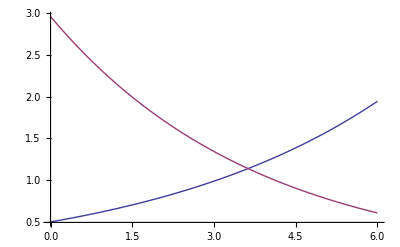

```mathematica
Plot[{a*b^t/.{a->0.5061360022826485,b->1.2513735255802725},a*b^(-t)/.{a->2.9540625116337824,b->1.299878796279082}},{t,0,6}]
```